```mathematica
NotebookEvaluate["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/00_SplinePack-034.nb"]//Quiet;

Get[URLDownload["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/TP_ImProc_01-m101.wl"]]//Quiet;

Get[URLDownload["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/TP_ImProc_01-m101.wl"]]//Quiet;
```

Null[[3]].Null[[2]].Null[[1]] Null[[4]]:Null[[5]]:Null[[6]]    (FileByteCount[] Bytes)

Null[[3]].Null[[2]].Null[[1]] Null[[4]]:Null[[5]]:Null[[6]]    (FileByteCount[] Bytes)

Null[[3]].Null[[2]].Null[[1]] Null[[4]]:Null[[5]]:Null[[6]]    (FileByteCount[] Bytes)

```mathematica
Clear[ToEnglish,Z,newID]
{ToEnglish,Z} = Get[URLDownload["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/EmissionRatePlotData.dat"]];
newID=Map[#[[1]]->StringJoin["P",ToString@#[[2]]]&,Transpose@{Union[Drop[Z[[All,1]],2]],Table[n,{n,Length@Union[Drop[Z[[All,1]],2]]}]}];
```

```mathematica
{
"Kl02","KP01","KP02","KP04","KP07","KP08","KP10","KP12","Ob02","Ob03","Ob04","Ob05","Ob06","Ob07","Ob09","Ob10","Ob11","Ob12","Qu01","Qu02","Qu03","Qu04","Qu06","Qu07","Qu10","Qu12","Qu14","Qu15","Qu16","Qu17","Qu18","Qu20"
}/.ToEnglish
WallLossGroupSupplementaryFigureS3 = SortBy[%/.newID,ToExpression[StringDrop[#,1]]&]
```

{C2,S1,S2,S4,S7,S8,S10,S12,O2,O3,O4,O5,O6,O7,O9,O10,O11,O12,F1,F2,F3,F4,F6,F7,F10,F12,F14,F15,F16,F17,F18,F20}

{P1,P2,P3,P5,P7,P8,P9,P10,P11,P13,P14,P15,P16,P18,P19,P21,P22,P23,P24,P25,P26,P27,P28,P29,P31,P32,P33,P35,P36,P38,P41,P42}

```mathematica
Clear[e,f,F,G,h,M,n,P,p,Q,q,R,s,μ,σ]
```

```mathematica
{M,G,h} = Get[URLDownload[F="https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-speaking-masks/Fig/TaskPlots/P-s/Breathing.dat"]];
```

```mathematica
Extract[G,Map[ReplacePart[#,1,-1]&,Position[G,Style]]]
Length[%]
```

{P40,P30,P37,P23,P31,P5,P41,P1,P24,P35,P8,P16,P19,P10,P22,P25,P15,P2,P42,P11,P26,P28,P13,P4,P7,P29,P9,P14,P32,P20,P33,P18,P43,P34,P12}

35

```mathematica
Complement[%%,WallLossGroupSupplementaryFigureS3]
```

{P12,P20,P30,P34,P37,P4,P40,P43}

```mathematica
Complement[WallLossGroupSupplementaryFigureS3,%%%]
```

{P21,P27,P3,P36,P38}

```mathematica
n =   Length[M]
μ = First/@M
σ =   Last/@M
OrderedQ[μ]
```

35

{-199.,-187.,-157.,-150.,-145.,-127.,-105.,-98.,-48.,-44.,-11.,-2.,-1.,21.,21.,23.,39.,48.,48.,86.,93.,117.,119.,149.,181.,181.,200.,204.,228.,274.,296.,350.,455.,559.,589.}

{335.,432.,302.,196.,266.,237.,151.,171.,198.,210.,196.,317.,79.,124.,244.,166.,213.,35.,164.,191.,95.,304.,151.,368.,209.,223.,83.,140.,153.,317.,224.,175.,302.,443.,354.}

True

```mathematica
Q = LogNormalDistribution[e,s];
startpar = FindDistributionParameters[Select[μ,Positive],Q];
p = N[Range[n]/(1+n)];
q = Quantile[Q,p];
f = μ-q;
f /= σ;
f = f.f;
f = FindMinimum[f,List@@@startpar];
Q = Q/.Last[f];
```

Measurement | TaskPlots
P-s
Breathing
n | 35
p-value (χ^2) | 1.05506×10^-8
Distribution | LogNormalDistribution[4.10138,1.36679]
Mode | 9.3304
Median | 60.4239
Mean | 153.767
Quartiles | 24.0348
60.4239
151.907
StandardDeviation | 359.828

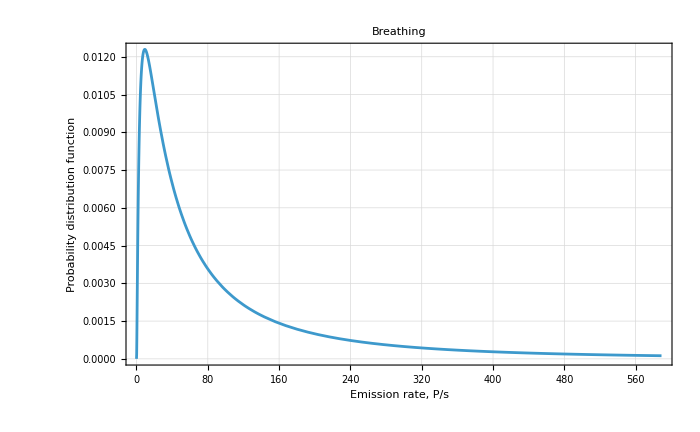

```mathematica
P = {Median,Mean,Quartiles,StandardDeviation};
P = Rule@@@Transpose[{ToString/@P,Map[#[Q]&,P]}];
PrependTo[P,"Mode"->("Median"^3/"Mean"^2)/.P];                                      (*    gilt nur für die LogNormalVerteilung    *)
PrependTo[P,"Distribution"->Q];
PrependTo[P,"p-value (χ^2)"->CDF[ChiSquareDistribution[n-2],First[f]]];
PrependTo[P,"n"->n];
PrependTo[P,"Measurement"->(taskname=Take[StringSplit[F,{".","/"}],{-4,-2}])];
TableForm[List@@@P]

Plot[
PDF[Q,x],{x,0,Last[μ]},
Frame->True,
FrameLabel->{Last[FrameLabel/.Rest[List@@G]],"Probability distribution function"},
GridLines->Automatic,
ImageSize->700,
LabelStyle->{
FontColor->GrayLevel[0],
FontFamily->"Lucida Sans Unicode",
FontSlant->"Plain",
FontWeight->"Plain",
FontSize->14},
PlotLabel->Last["Measurement"/.P],
PlotRange->All]
```

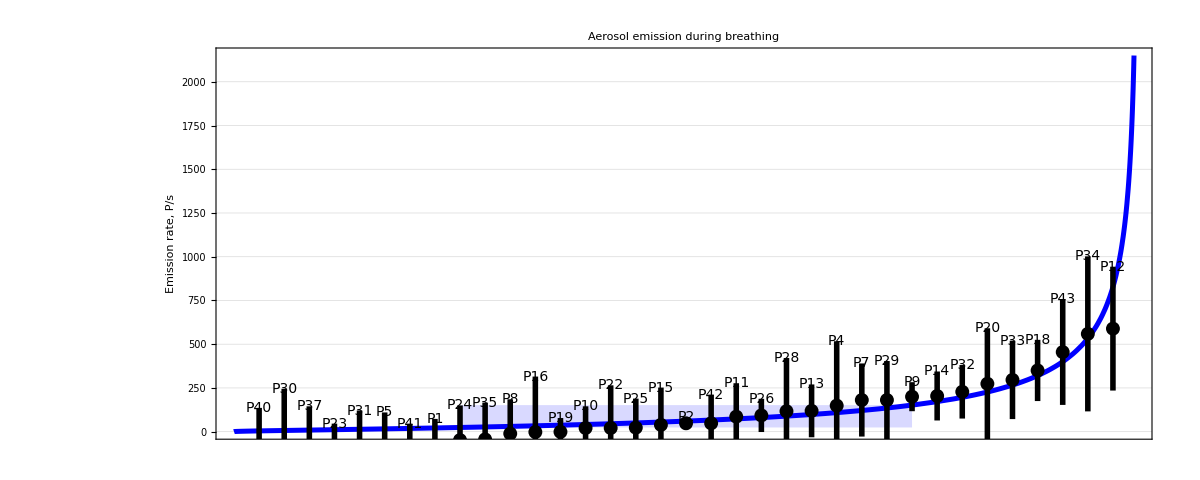

```mathematica
Clear[f];
f[k_] := Quantile[Q,k/(1+n)];
L = Plot[f[x],{x,0,n+1},DisplayFunction->Identity,PlotRange->(PlotRange/.Rest[List@@G])];
L = Extract[L,Most[First[Position[L,Line]]]];
R = Transpose[{(1+n)*{1,3}/4.,("Quartiles"/.P)[[{1,3}]]}];
h = ReplacePart[G,
Prepend[G[[1]],
{Blue,
{Opacity[0.15],Rectangle@@R},
{Thickness[0.003],L}}
],1];
h = h/.{
"Arial"->"Lucida Sans Unicode",
(FontSize -> 16)->(FontSize -> 14)}
```

```mathematica
Export[StringJoin[NotebookDirectory[],"\\output directory\\",
"Breathing","_lognormal.svg"],h]
```

C:\Users\mona_\Downloads\upload aerosol study 2020\\output directory\Breathing_lognormal.svg

```mathematica
(*

ENDE

*)
```

```mathematica
Clear[L,k,n]
```

```mathematica
L = p^k*(1-p)^(1+n-k)
```

(1-p)^(1-k+n) p^k

```mathematica
Solve[D[Log[L],p]/L==0,p]
```

{{p→ConditionalExpression[0, Re[k]<-1]},{p→ConditionalExpression[1, Re[n]<-2+Re[k]]},{p→k/(1+n)}}